### Drag Racer Accelerating for 5 Seconds

A drag racer waits at the starting line until t=5. It accelerates madly from t=5 to t=10. After t=10, it coasts at constant speed. Below is a function that describes its position.

```mathematica
position[t_]:= Piecewise[{{0,t⩽5},{6(t-5)^2/2, t>5 && t<10}, {30(t-10) +75, t⩾10}}]
```

Here is a plot of what the drag racer is doing from t=3  to t=13.

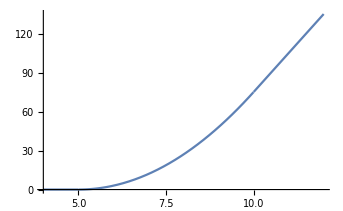

```mathematica
Plot[position[x],{x,4,12}]
```

Here is a table of the positions of the drag racer from t=4 to t=12.

```mathematica
tableOfValues=Table[{t, position[t], "        ", "        "}, {t,4, 12, 0.5}];
```

```mathematica
Grid[Prepend[tableOfValues, {"time", "position", "   velocity   ", "acceleration"}], Frame->All]
```

time | position |    velocity    | acceleration
4. | 0 |          |         
4.5 | 0 |          |         
5. | 0 |          |         
5.5 | 0.75 |          |         
6. | 3. |          |         
6.5 | 6.75 |          |         
7. | 12. |          |         
7.5 | 18.75 |          |         
8. | 27. |          |         
8.5 | 36.75 |          |         
9. | 48. |          |         
9.5 | 60.75 |          |         
10. | 75. |          |         
10.5 | 90. |          |         
11. | 105. |          |         
11.5 | 120. |          |         
12. | 135. |          |

Fill in the third column of this table with approximations to the derivative of the position. This is called the velocity. Plot the velocities on the empty plot below.

```mathematica
Plot[{}, {t, 3, 12}, PlotRange->{{3, 12},{0, 30}}]
```

-Graphics-

Go back to the table. Fill in the fourth column of the table. This column will contain approximations to the derivative of the velocity. This is called the acceleration. Plot the accelerations on the empty plot below.

```mathematica
Plot[{}, {t, 3, 12}, PlotRange->{{3, 12},{0, 10}}]
```

-Graphics-